```mathematica
τ1=0.000014355
τ2=0.0000172822
H[s]= s/(s+(1/τ1))*1/τ2*1/(s+(1/τ2))*1/s*1.02
```

0.000014355

0.0000162822

62645.1/((61416.8+s) (69662.1+s))

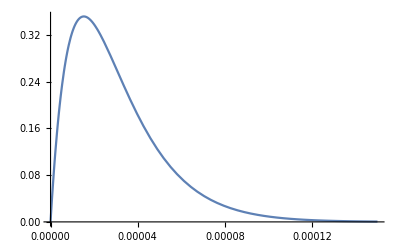

```mathematica
Plot[InverseLaplaceTransform[H[s], s, t], {t, 0, 0.00015}, PlotRange->All]
```

```mathematica
b=InverseLaplaceTransform[H[s], s, t];
list1=Table[{t,b }, {t, 0, 0.00015, 0.000001}];
```

```mathematica
Export["C:\\Users\\berto\\NotSync\\GitHub\\Laboratorio_3\\Esperienza_03\\Dati\\2_1_teor.txt", list1, "Table"];
```

```mathematica
Plot[H[100]]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[H[100]]